# What Makes an Attractive Image?

Artlandia^® Demo Series

Copyright © 1998-2001 by Artlandia, Inc. This notebook demonstrates some of the designer tools available in Artlandia. The notebook may be copied or distributed freely, as long as it is distributed in its entirety. All other rights reserved. In particular, reproduction of individual images without the prior written permission of the copyright holder is expressly prohibited. Questions and comments are welcome at info@artlandia.com. More information about Artlandia and related products is available at http://www.artlandia.com. For more information about the Graphica books visit http://www.graphica.com. Artlandia is a registered trademark of Artlandia, Inc. Graphica is a trademark of Wolfram Media, Inc. All other product names are trademarks of their producers. The notebook is based on the chapter by the same title in the Graphica 2 book.

A new and amazing instrument has come into the hands of artists. In the past, graphic art had to be painstakingly created from individual primitives such as lines, polygons, or brush strokes. But now, with Mathematica, an artist can think at a higher level, and create complex objects all at once at the click of a mouse. Mathematica makes this possible with its ability to describe processes as well as objects. Instead of having to specify directly where each element in an image should go, an artist can specify an algorithm, and Mathematica then forms the final image. Artlandia, a Mathematica-based application for creative graphic design, provides such tools. In this notebook, we illustrate the graphical "character" of several fundamental random processes that Artlandia puts at your fingertips, and show you how to apply these processes to enhance the attractiveness of your images.

## Signature of Randomness

The characteristic property of a random process—or an array of random numbers—is its time or space correlation, as desribed by the power spectrum. There are three fundamental types of random processes that describe the majority of random processes in nature: those exhibiting the white or flat (i.e., independent of frequency f) spectrum, the flicker (or 1/f-type) spectrum, and the random-walk (or 1/f^2-type) spectrum. In nonmathematical language, these power spectra describe just how "random" a random sequence is. The correlation is absent in white noise, becomes visible in 1/f-noise, and dominates random-walk noise.

Artlandia makes these arrays available as the RandomArray, NaturalArray, and RandomWalkArray functions. The name NaturalArray indicates both that the 1/f spectrum is the most widespread in nature and that in many cases it seems to yield the most harmonic images. In fact, NaturalArray is chosen as the default array for many Artlandia functions. Let's familiarize ourselves with some of the properties of the random arrays.

We start by loading Artlandia.

```mathematica
<<Artlandia`
```

To graphically illustrate statistical properties of the random arrays we construct random Truchet patterns based on the Sebastien Truchet's tiling (see, e.g., E. H. Gombrich, The Sense of Order. Cornell University Press, Ithaca, NY: 1979). The Truchet function creates two types of tiles, each formed by a pair of quarter circles. Depending on the value of the first argument, which can be either 0 or 1, the centers of the arcs are arranged at either the top left and lower right, or top right and lower left.

This defines the Truchet function.

```mathematica
Truchet[0,{x_,y_}]:={Circle[{x,y+1},1/2,{-π/2,0}],Circle[{x+1,y},1/2,{π/2,π}]}
```

```mathematica
Truchet[1,{x_,y_}]:={Circle[{x,y},1/2,{0,π/2}],Circle[{x+1,y+1},1/2,{π,(3 π)/2}]}
```

Here are the two tiles.

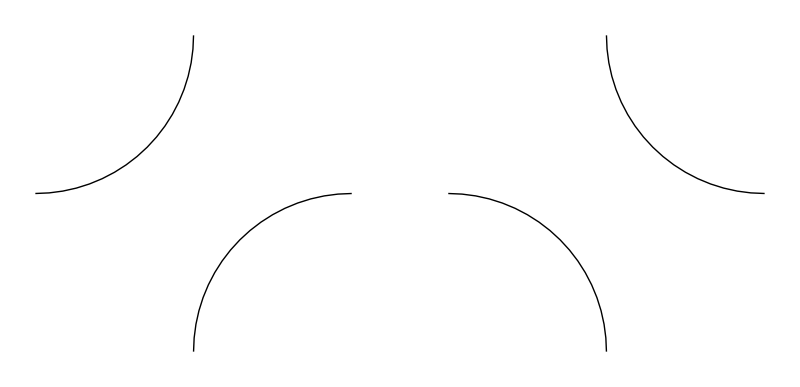

```mathematica
Show[GraphicsRow[Graphics[Truchet[#,{0,0}],AspectRatio->1]&/@{0,1}],GraphicsSpacing->.75]
```

This function converts a matrix of zeros and ones into the Truchet tiling.

```mathematica
TruchetMatrix[mat_]:=MapIndexed[Truchet,mat,{2}]
```

Here are the mazes generated by the RandomArray, NaturalArray, and RandomWalkArray functions.

```mathematica
Show[Graphics[TruchetMatrix[ArrayOf[{0,1},{30,30},GeneratingFunction->#]],AspectRatio->Automatic]]&/@{RandomArray,NaturalArray,RandomWalkArray};
```

Notice how the correlation properties of the random arrays exhibit themselves in the maze patterns: the RandomArray maze has on average the shortest and the RandomWalkArray one the longest connected paths. More visual images of "noise faces" can be found on the Artlandia web site at http://www.artlandia.com/software/lab.

## "Natural" Truchets

Several similar "natural" mazes of different periods, one overlaid on the other, form a beautiful lace image that appears in the Graphica 2 book. Here is the algorithm to generate a simplified lace that consists of n = 12 tilings. Artlandia users can reproduce the larger image in the book with n = 30.

```mathematica
n=12;
```

The color palette for the pattern consists of a spectrum of n shades from RGBColor[.8,1,1] (a very light blue) to white. Note that, by default, the Shades function automatically creates the natural distribution of colors in the given color range.

```mathematica
colors=Shades[{RGBColor[.8,1,1],White},n];
```

Here is the superimposition of n tilings of different scales. The coarser tilings are drawn with thicker lines. CombineGraphics puts the tilings into the same rectangle.

```mathematica
Show[CombineGraphics[MapThread[Graphics[{AbsoluteThickness[10./#],#2,TruchetMatrix[ArrayOf[{0,1},{#,#}]]},AspectRatio->1,PlotRange->All]&,{Round[NaturalArray[n,{5,20}  ]],colors}],Background->CornflowerBlue,ToSameSize->Automatic],AspectRatio->1];
```